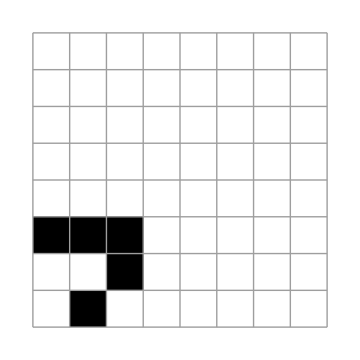

```mathematica
plt=Magnify[ArrayPlot[#,Frame->False,Mesh->True] ,.3]&;
X0=({
    {0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{0,0,0,0,0,0,0,0}
,{1,1,1,0,0,0,0,0}
,{0,0,1,0,0,0,0,0}
,{0,1,0,0,0,0,0,0}
});
X0//plt
```

Questions like this are readily expressed as sat problems

Each state t is a vector of boolean variables, (we could flatten X0)

Each transition relation can be represented by a set of m clauses that must be satisfied.

these clauses are connectives between the Boolean variables

this is hard to imagine slash vizualize

This set of clauses T involve 2n boolean variables, one variable for each grid cell in the current state

one variable for each cell in the next state, the primed state

Then the existence of sequence 33 is equivalent to the satisfiability of m r clauses.

each transition requires m clauses and there are r transitions

T[X_0,x_1]∧…∧T[X_(r-1),x_r]

amazingly we are framing LIFE as a sat problem

this section shows you how to frame a diverse set of problems as sat problems

arbitrary abstract state transition sequence 33:

X_0→…→X_R

the existence of sequence 33 is equivalent to the satisfiability of m r clauses in the n times r plus 1 variables

I love music that captures a sense of the profound, beyond human comprehension like plaid and bleed by meshuggah and vicarious.

{x_tj\[Conditioned]0≤t≤r,1≤j≤n}

this is just a table in mathematica

```mathematica
Clear[x];
n=2;
r=3;
Table[Subscript[x, {t,j}] ,{t,0,r},{j,1,n}]//Grid
```

x_{0,1} | x_{0,2}
x_{1,1} | x_{1,2}
x_{2,1} | x_{2,2}
x_{3,1} | x_{3,2}

We have essentially unrolled the sequence 33 into r copies of the transition relation

using the set of variables x sub t j for teeth state X sub t

Additional clauses can now be added to specify constraints the initial state X zero and or the finial state X r

as well as any other conditions that we want to impose on the sequence

We have essentially unrolled the sequence 33 into r copies of the transition relation

using variables x sub t for the set of states X sub t

there are r states

an arbitrary or general state is state t

t iterates from zero to r

This general setup is called bounded model checking, because we are using it to check properties of a model (a transition relation), and because we are considering only sequences that have a bounded number of transitions, r

John Conways fascinating Game of Life provides a particularly instructive set of examples that illustrates basic principles of bounded model checking.

Gretty is getting all angry like Charlie. The neural machinery is low in some vital transmitter. Don't take it to heart man.

Pour the rest of your cognition into this crusade into the Platonic realm.

The states X of this game are two-dimensional bitmaps, corresponding to arrays of square cells that are either alive or dead.

Every bitmap X has a unique successor X prime, determined by the action of a simple 3 by 3 cellular automaton

Suppose some cell has the eight neighbors north west, north, north east, west, east, south west, south, south east and let nu equals the sum of these boolean variables which goes out of the boolean number system into the integers.

Then x is alive at time t plus 1 if and only if either nu equals 3 or (nu equals 2 in conjunction with x being already alive at time t.

Equivalently, the transition rule, x prime equals the sum